# Rubel’s universal differential equation

## The starting point, g(x), is a C^∞ function which vanishes outside the interval (-1,+1) :

```mathematica
g[x_]:=Piecewise[{{0,x<-1},{ Exp[-1/(1-x^ 2)],-1<x<1},{0,x>1}}]
```

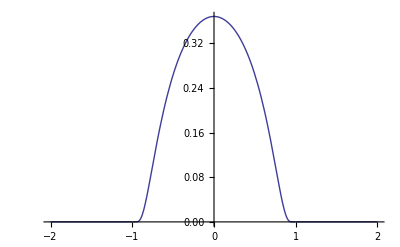

```mathematica
Plot[g[x],{x,-2,2}]
```

## Its primitive is constant outside the interval (-1,+1), resp. f(-1)=0 if x<-1 and f(1)=Ω if x>1 :

```mathematica
h[x_]:=NIntegrate[g[u],{u,-1,x}]
```

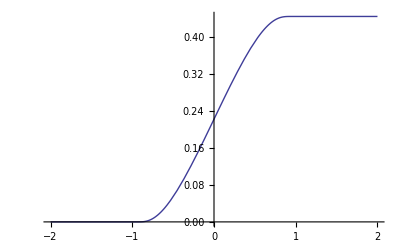

```mathematica
Plot[h[x],{x,-2,2}]
```

## Ω is a well-defined real (no closed form is known) :

```mathematica
Ω=NIntegrate[g[u],{u,-1,1},WorkingPrecision->24]
```

0.443993816168079437823049

## Rubel’s model, f(x), fits the given function y(x) in the interval (a,b) (exactly at the ends of the interval) :

```mathematica
f[x_,a_,b_,ya_,yb_]:=(yb-ya)/Ω∫_-1^((2x-(a+b))/(b-a)) Exp[-1/(1-u^ 2)]ⅆu+ya
```

## Example of a continuous junction between two consecutive intervals, say (0,1) and (1,3/2) (numerical integration is needed) :

```mathematica
fnum[x_,a_,b_,ya_,yb_]:=(yb-ya)/Ω NIntegrate[Exp[-1/(1-u^ 2)],{u,-1,(2x-(a+b))/(b-a)}]+ya
```

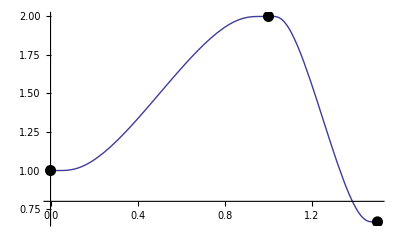

```mathematica
Plot[Piecewise[{{fnum[x,0,1,1,2],x<1},{ fnum[x,1,3/2,2,2/3],1<x}}],{x,0,3/2},Epilog->{PointSize[0.02],Point[{0,1}],Point[{1,2}],Point[{3/2,2/3}]}]
```

## Differential equation fullfilled by the model function, f(x), whatever the interval :

```mathematica
Clear[Ω]             (*Let us forget the numerical value of Ω*)
```

```mathematica
y[x_]:=(yb-ya)/Ω∫_-1^s[x] Exp[-1/(1-u^ 2)]ⅆu+ya
```

```mathematica
{y'[x],y''[x],y'''[x],y''''[x]}/.{s'[x]->2/(b-a),s''[x]->0,s'''[x]->0,s''''[x]->0}//Simplify
```

{(2 ⅇ^(1/(-1+s[x]^2)) (ya-yb))/((a-b) Ω),(8 ⅇ^(1/(-1+s[x]^2)) (ya-yb) s[x])/((a-b)^2 Ω (-1+s[x]^2)^2),(16 ⅇ^(1/(-1+s[x]^2)) (ya-yb) (-1+3 s[x]^4))/((a-b)^3 Ω (-1+s[x]^2)^4),(64 ⅇ^(1/(-1+s[x]^2)) (ya-yb) s[x] (3-10 s[x]^2+3 s[x]^4+6 s[x]^6))/((a-b)^4 Ω (-1+s[x]^2)^6)}

Set W=(2 ⅇ^(1/(-1+s[x]^2)) (ya-yb))/((a-b) Ω) and  eliminate W, a, b  and s[x]  between the five equations :

```mathematica
Eliminate[{f1== W ,f2==(4W  s[x])/((a-b)  (-1+s[x]^2)^2),f3==(8W  (-1+3 s[x]^4))/((a-b)^2  (-1+s[x]^2)^4),f4==(32W  s[x] (3-10 s[x]^2+3 s[x]^4+6 s[x]^6))/((a-b)^3  (-1+s[x]^2)^6),s[x]==(2x-(a+b))/(b-a)},{W,a,b,s[x]}]
```

$Aborted

Mathematica needs a little help.  Obviously, the two first equations allow to eliminate W and (a-b) respectively :

```mathematica
Eliminate[{f3==(f2^2  (-1+3 s[x]^4))/(2f1 s[x]^2),f4==(f2^3  s[x] (3-10 s[x]^2+3 s[x]^4+6 s[x]^6))/(2 f1^2 s[x]^3)},{s[x]}]
```

12 f2 f3^3-6 f2^2 f3 f4+f3^2 ((29 f2^3)/f1+4 f1 f4)==f2 ((12 f2^6)/f1^3+(24 f2^3 f4)/f1+3 f1 f4^2)&&f1≠0

```mathematica
Numerator[Together[12 f2 f3^3-6 f2^2 f3 f4+f3^2 ((29 f2^3)/f1+4 f1 f4)-f2 ((12 f2^6)/f1^3+(24 f2^3 f4)/f1+3 f1 f4^2)]]
```

-12 f2^7+29 f1^2 f2^3 f3^2+12 f1^3 f2 f3^3-24 f1^2 f2^4 f4-6 f1^3 f2^2 f3 f4+4 f1^4 f3^2 f4-3 f1^4 f2 f4^2

This is Rubel’s equation where fk stands for the kth derivative of y(x).